#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
(*Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]*)
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];
parity="-";
jJ=0.5;
mJs=Range[-jJ,jJ,1];
mom =0.001/198;
```

```mathematica
ClearAll;
ImgSize=900;
SetDirectory["/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan/results"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan/results

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["discarded: ",n," ",Select[es[[1]],#<cutoff&]];n=Length[Select[es[[1]],#<cutoff&]];ovsq=DiagonalMatrix[SparseArray[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]]];ovsqi=DiagonalMatrix[SparseArray[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

```mathematica
mat={{2,2,3},{2,4,5},{3,5,10.}}
```

{{2,2,3},{2,4,5},{3,5,10.}}

```mathematica
mat//MatrixForm
```

(2 | 2 | 3
2 | 4 | 5
3 | 5 | 10.)

```mathematica
N[Eigenvalues[mat]]
```

{13.9166,1.32306,0.760354}

```mathematica
{msq,msqi}=matSqrts[mat,1]
```

min/max: {0.760354,13.9166}

discarded: 1 {0.760354}

{{{1.07816,1.77885,3.09675},{-0.575241,-0.763987,0.639126}},{{0.0774728,-0.434781},{0.127822,-0.577439},{0.222522,0.483067}}}

```mathematica
Chop[Transpose[msqi].mat.msqi]//MatrixForm
```

(1. | 0
0 | 1.)

### Read LHS ⟨ ϕ_(3He)^n|(Ĥ)_(V18+UIX)|ϕ_(3He)^m ⟩, m,n∈{1,N_He3}

```mathematica
HeNormHamMat=ReadList["./mat_npp0.5^+",Number];
HeBasisDim=HeNormHamMat[[1]];
HeNorm=ArrayReshape[HeNormHamMat[[2;;HeBasisDim^2+1]],{HeBasisDim,HeBasisDim}];HeHam=ArrayReshape[HeNormHamMat[[HeBasisDim^2+2;;2 HeBasisDim^2+1]],{HeBasisDim,HeBasisDim}];
```

```mathematica
{HeNmh,HeNmhi}=matSqrts[HeNorm,0];
```

min/max: {0.100848,2.80077}

discarded: 0 {}

```mathematica
tst=Transpose[HeNmhi].HeNorm.HeNmhi;
```

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

```mathematica
tv=Transpose[Eigensystem[HeNorm]][[-2]];
```

```mathematica
tv[[1]]
```

0.163783

```mathematica
Chop[HeHam.tv[[2]],10^-6]
```

{5.19965,-10.8103,-0.033715,-0.153788,0.284393,0.0864905,0.968004,0.315916,19.224,-18.9706,-1.55605,1.36363,-0.371933,1.41897,-0.158317,0.357799}

```mathematica
tv=Transpose[Eigensystem[HeNorm]][[-4]];
```

```mathematica
tv[[1]]
```

0.347352

```mathematica
Chop[HeHam.tv[[2]],10^-7]
```

{6.80512,-14.211,-0.0628483,-0.285526,0.459002,0.141189,1.72613,0.571282,25.1087,-24.7789,7.46216,-7.03016,-2.77218,-4.29252,-0.593338,-1.11261}

#### The real calculation

Set a sensible cut-off

```mathematica
{HeNmh,HeNmhi}=matSqrts[HeNorm,2 10^-10];
```

min/max: {0.100848,2.80077}

discarded: 0 {}

```mathematica
{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[HeNmhi].HeHam.HeNmhi;tst=(tst+Transpose[tst])/2]],#1[[1]]<#2[[1]]&][[1]];
```

```mathematica
e0
```

0.166239

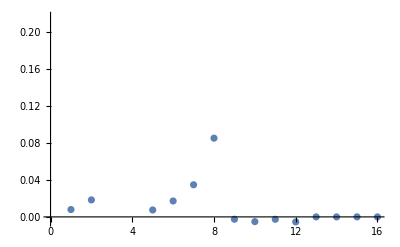

```mathematica
fullv0=Normalize[Transpose[HeNmh].v0];
ListPlot[fullv0]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
LitNormHamMat=ReadList["./mat_"<>ToString[jJ]<>"^"<>parity,Number];
LITbasisDim=LitNormHamMat[[1]];
LitNorm=ArrayReshape[LitNormHamMat[[2;;LITbasisDim^2+1]],{LITbasisDim,LITbasisDim}];LitHam=ArrayReshape[LitNormHamMat[[LITbasisDim^2+2;;2 LITbasisDim^2+1]],{LITbasisDim,LITbasisDim}];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = 16

#### Read RHS ⟨ ϕ_(lit+He3)^n|O_Lm_L|ϕ_(lit+He3)^m ⟩, n,m∈{1,N_LIT/n_k+N_He3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_inhomo*"],"_"][[All,1]]]];
ks=Range[0,nk];
mJ=mJs[[1]];
mL=mLs[[1]];
If[Abs[mJ-mL]≤1/2,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[mL]<>".log"&/@ks,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[-mL]<>".log"&/@ks
]

inhomos=SparseArray[ReadList[#,Number,RecordLists->True]]&/@files;
CouplingMatrices=SparseArray[ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]]&/@inhomos;
```

{./0_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./1_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./2_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./3_inhomo1-1_J0.5_mJ-0.5-mL-1.log}

```mathematica
Dimensions[inhomos[[1]]]
Dimensions[CouplingMatrices[[1]]]
```

{400,1}

{20,20}

#### Read expansion coefficients of He3 |He3 ⟩=∑_(m=1)^N_He3 c_m·|ϕ_He3^m ⟩

```mathematica
(*coeffs=RandomReal[{0,10^(-1)},HeBasisDim];*)
coeffs=fullv0;
Print["N_He3 = ",Length[coeffs]," = ",HeBasisDim,"  ⟨0|0⟩ = ",Norm[coeffs]];
```

N_He3 = 16 = 16  ⟨0|0⟩ = 1.

#### calculate the components of the RHS inhomogeneity vector by summing up the ME’s of one row with each column weighted by the corresponding |He3 ⟩ coefficient

```mathematica
CouplingBloxx=#[[HeBasisDim+1;;,;;HeBasisDim]]&/@CouplingMatrices;
RHSComponents=#.coeffs&/@CouplingBloxx;
RHSVector=Flatten[RHSComponents];
If[Length[RHSVector]≠LITbasisDim,Print["LIT state dimension of RHS("<>ToString[Length[RHSVector]]<>") and LHS("<>ToString[LITbasisDim]<>") inconsistent!"]]
Dimensions[CouplingBloxx[[4]]]
```

{4,16}

```mathematica
Normal[CouplingBloxx[[1]]]//MatrixForm
```

(-2.111×10^-7 | -2.199×10^-7 | -0.003251 | -0.05169 | -2.282×10^-7 | -2.368×10^-7 | -0.00003219 | -0.00004117 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-2.186×10^-7 | -2.277×10^-7 | -0.005177 | -0.2988 | -2.361×10^-7 | -2.451×10^-7 | -0.0000349 | -0.00004496 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0008368 | -0.001342 | -4.696 | -179.2 | -0.0008124 | -0.001252 | -0.0245 | -0.04204 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.01292 | -0.07525 | -43.69 | -2523. | -0.00875 | -0.03203 | -0.2297 | -0.907 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
dims=Dimensions[CouplingBloxx];
CouplingBlock=ArrayReshape[CouplingBloxx,{dims[[3]],dims[[3]]}];
Chop[CouplingBlock,10^-10]//MatrixForm
Chop[CouplingBlock,10^-10].fullv0//MatrixForm
(*CouplingBlock[[162,All]]==Normal[CouplingBloxx[[2]][[-1,All]]]*)
```

(-2.111×10^-7 | -2.199×10^-7 | -0.003251 | -0.05169 | -2.282×10^-7 | -2.368×10^-7 | -0.00003219 | -0.00004117 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2.186×10^-7 | -2.277×10^-7 | -0.005177 | -0.2988 | -2.361×10^-7 | -2.451×10^-7 | -0.0000349 | -0.00004496 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0008368 | -0.001342 | -4.696 | -179.2 | -0.0008124 | -0.001252 | -0.0245 | -0.04204 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.01292 | -0.07525 | -43.69 | -2523. | -0.00875 | -0.03203 | -0.2297 | -0.907 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.673×10^-8 | 5.903×10^-8 | 0.001588 | 0.01755 | -2.2×10^-8 | -2.281×10^-8 | -3.091×10^-6 | -3.939×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.75×10^-8 | 5.985×10^-8 | 0.002416 | 0.0634 | -2.269×10^-8 | -2.353×10^-8 | -3.34×10^-6 | -4.286×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.522×10^-6 | -6.03×10^-6 | 0.04145 | 0.4727 | -1.105×10^-6 | -1.201×10^-6 | -0.00007739 | -0.000102 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.358×10^-6 | -8.095×10^-6 | 0.06362 | 1.669 | -1.382×10^-6 | -1.514×10^-6 | -0.00009738 | -0.0001308 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.291×10^-9 | -1.526×10^-9 | -4.973×10^-7 | -3.797×10^-7 | -2.487×10^-7 | -2.576×10^-7 | -5.623×10^-6 | -6.218×10^-6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.526×10^-9 | -6.862×10^-10 | -3.422×10^-7 | -1.767×10^-7 | -2.601×10^-7 | -2.694×10^-7 | -5.999×10^-6 | -6.645×10^-6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.973×10^-7 | -3.422×10^-7 | -0.000109 | -0.00008548 | -0.0000531 | -0.00005677 | -0.001208 | -0.001375
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.797×10^-7 | -1.768×10^-7 | -0.00008548 | -0.00004556 | -0.00006356 | -0.00006817 | -0.001471 | -0.001682
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.×10^-9 | 4.162×10^-9 | 1.097×10^-6 | 9.171×10^-7 | -7.086×10^-7 | -7.398×10^-7 | -0.00001102 | -0.00001246
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.152×10^-9 | 2.064×10^-9 | 8.292×10^-7 | 4.98×10^-7 | -7.492×10^-7 | -7.825×10^-7 | -0.00001206 | -0.00001366
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.731×10^-7 | 3.373×10^-7 | 0.00008721 | 0.0000746 | -0.0001083 | -0.0001161 | -0.001165 | -0.001349
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.587×10^-7 | 1.835×10^-7 | 0.0000719 | 0.00004433 | -0.0001274 | -0.0001369 | -0.001413 | -0.001644)

(-0.0476457
-0.269446
-162.293
-2275.18
0.0163866
0.0577461
0.440786
1.52017
3.09884×10^-9
1.57595×10^-9
6.92151×10^-7
4.02082×10^-7
-8.35048×10^-9
-5.42321×10^-9
-6.87563×10^-7
-4.94917×10^-7)

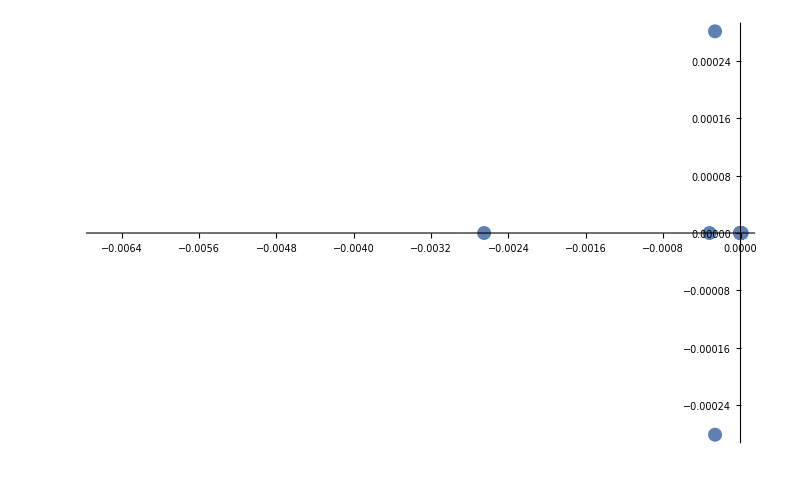

```mathematica
es=Eigensystem[CouplingBlock];
ListPlot[Transpose[{Re[es[[1]]],Im[es[[1]]]}]](*n=Length[Select[es[[1]],#<cutoff&]];Print["discarded: ",n," ",Select[es[[1]],#<cutoff&]];n=Length[Select[es[[1]],#<cutoff&]];ovsq=DiagonalMatrix[SparseArray[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]]];ovsqi=DiagonalMatrix[SparseArray[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=5.;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
threshold=10^(-10);
testfu=0;
inhomo=(2/mom) RHSVector;
```

```mathematica
Clear[normreg];
normreg[threshold_]:=Block[
{es=Eigensystem[LitNorm],μ,transf,μs,Or},
{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];
If[Dimensions[μ]<Dimensions[es[[1]]],
{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];
,{μs,Or}={{},{}}];
{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}];

Clear[decompose];
decompose[threshold_]:= Block[{Oμ,Or,μs,oλs,otrf},
{Oμ,Or,μs}=normreg[threshold];{λs,trf}=Eigensystem[(Transpose[Oμ].LitHam).Oμ];{λs,trf.(Transpose[Oμ].inhomo)}
];
Clear[litcomp];
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@((Abs[#[[2]]]^2/((#[[1]]-e0-σRe)^2+σI^2))&/@λscf)];
```

```mathematica
testcompo={};testfu=0;
testfu+=Evaluate[litcomp[threshold]];
tmps=Transpose[decompose[threshold]];
testcompo=AppendTo[testcompo,Re[tmps]];

LIT=(-1)^(jJ-0.5) testfu;
LITcompo=Flatten[testcompo,1];

LITcompo=Transpose[{LITcompo[[All,1]],Re[(-1)^(jJ-0.5) LITcompo[[All,2]]]}];
```

```mathematica
testcompo;
```

```mathematica
Plot[LIT,{σRe,-10,120},PlotRange->{Automatic,Full},MaxRecursion->0,PlotPoints->500,MeshFunctions->{#&},Mesh->60,MeshStyle->PointSize[Large],
PlotLabel->"EV basis N_ev > "<>ToString[N[threshold],TraditionalForm]<>"   σ_I = "<>ToString[σI],AxesLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},ImageSize->ImgSize,PlotLegends->{"J="<>ToString[jJ]},ImageSize->ImgSize]
```

-Graphics-

```mathematica
maxi=1.05 Max[Select[LITcompo,#[[1]]<100&][[All,2]]];
mini=0.95 Min[Select[LITcompo,#[[1]]<100&][[All,2]]];
strengthfunctionBare=Transpose[{LITcompo[[All,1]],(LITcompo[[All,2]]^2)}];
ListPlot[strengthfunctionBare,Joined->False,PlotMarkers->Automatic,Filling->Axis,FillingStyle->Green,PlotRange->{{-10,120},All},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[ks]]]]&[Floor[i-1,1]+1],{i,1,Length[ks]}],PlotLegends->{"I_n="<>ToString[jJ]},ImageSize->ImgSize]
```

-Graphics-

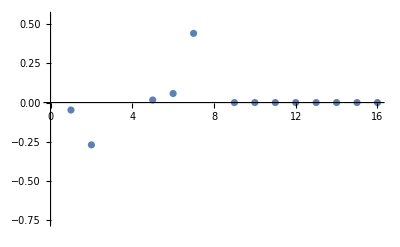

```mathematica
ListPlot[RHSVector]
```